# Classifying ECA by Their Initial State.

In this experiment, we will try to associate each automaton evolution string to its initialization.

The Sets

First, we get a random number of initialization of strings, with higher probability according to its BDM. Also, Let’s keep it small for now.

We will use an accuracy resolution of 16-bits for the inputs and 14-bits for the outputs.

```mathematica
toBinaryInt[n_,bits_]:=IntegerDigits[n,2,bits]
```

```mathematica
set = Range[2^12];
```

Computing the weights set using the square of the BDM of the binary representations of the strings.

```mathematica
SeedRandom[3012019]
class = RandomSample[set,10]
classB = toBinaryInt[#,12]&/@class
```

{704,3572,3067,3184,1939,2386,2896,205,828,3935}

{{0,0,1,0,1,1,0,0,0,0,0,0},{1,1,0,1,1,1,1,1,0,1,0,0},{1,0,1,1,1,1,1,1,1,0,1,1},{1,1,0,0,0,1,1,1,0,0,0,0},{0,1,1,1,1,0,0,1,0,0,1,1},{1,0,0,1,0,1,0,1,0,0,1,0},{1,0,1,1,0,1,0,1,0,0,0,0},{0,0,0,0,1,1,0,0,1,1,0,1},{0,0,1,1,0,0,1,1,1,1,0,0},{1,1,1,1,0,1,0,1,1,1,1,1}}

### Now, the Data Sets.

Let’s use 20 samples per class.

```mathematica
nSamples = 20;
size = 4;
```

```mathematica
SeedRandom[0103019]
TrainingSample = 
DeleteDuplicates@Catenate@Table[
Table[
With[
{aut =RandomInteger[128]},
(Rest@CellularAutomaton[aut,classB[[i]],size])->class[[i]]
]
,{j,nSamples}]
,{i,Length[class]}];

ValidationSample = 
DeleteDuplicates@Catenate@Table[
Table[
With[
{aut =RandomInteger[128]},
(Rest@CellularAutomaton[aut,classB[[i]],size])->class[[i]]
]
,{j,nSamples}]
,{i,Length[class]}];

TestSample = 
DeleteDuplicates@Catenate@Table[
Table[
With[
{aut =RandomInteger[128]},
(Rest@CellularAutomaton[aut,classB[[i]],size])->class[[i]]
]
,{j,nSamples}]
,{i,Length[class]}];
```

The data sets are composed of elements of the form:

```mathematica
ex=RandomChoice@TrainingSample
```

{{1,1,1,1,1,0,1,1,1,1,1,1},{0,0,0,0,0,1,1,0,0,0,0,0},{1,1,1,1,1,1,0,1,1,1,1,1},{0,0,0,0,0,0,1,1,0,0,0,0}}→704

Which means that the matrix:

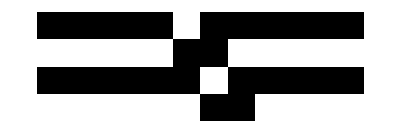

```mathematica
ArrayPlot@ex[[1]]
```

Was generated by the string

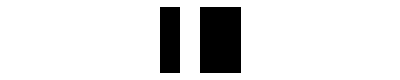

```mathematica
ArrayPlot@toBinaryInt[{ex[[2]]},16]
```

For a randomly selected automaton.

## Solving the Classification Problem With NN.

Let’s see if we can solve this problem with NN.

```mathematica
TrainingSample2 = ({#[[1]]}->#[[2]])&/@TrainingSample;
ValidationSample2 = ({#[[1]]}->#[[2]])&/@ValidationSample;
TestSample2 = ({#[[1]]}->#[[2]])&/@TestSample;
```

```mathematica
TrainingSample2[[1]]
```

{{{1,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,1,1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,1,1,1,0,0,0,0,0,0}}}→704

```mathematica
nn =  NetChain[{ ConvolutionLayer[12,{3,2}],Ramp,PoolingLayer[{2,9}],FlattenLayer[], LinearLayer[Length@class],SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",class}],"Input"-> {1,4,12}];
```

```mathematica
net = NetTrain[nn,TrainingSample2,ValidationSet->ValidationSample2, TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net, TestSample2, "Accuracy"]
```

0.174157

```mathematica
ClassifierMeasurements[net, TrainingSample2, "Accuracy"]
```

0.522727

Classification is barely above random choice.

Let’s see if a more general model performs better.

```mathematica
nn2 = NetChain[
{FlattenLayer[], 
LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[],Ramp,
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",class}],"Input"-> {4,12}
]
```

NetChain[<>]

```mathematica
SeedRandom[03012019]
net2 = NetTrain[nn2,TrainingSample,ValidationSet->ValidationSample, TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net2, TestSample, "Accuracy"]
```

0.601124

```mathematica
ClassifierMeasurements[net2, TrainingSample, "Accuracy"]
```

0.988636

It indeed does much better, but 60% is still a low value. I’m actually surprised that the network did this good, though.

Let’s see if a deeper model performs better.

```mathematica
nn3 = NetChain[
{FlattenLayer[], 
LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[],Ramp,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",class}],"Input"-> {4,12}
]
```

NetChain[<>]

```mathematica
net3 = NetTrain[nn3,TrainingSample,ValidationSet->ValidationSample, TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net3, TestSample, "Accuracy"]
```

0.578652

```mathematica
ClassifierMeasurements[net3, TrainingSample, "Accuracy"]
```

0.960227

It performed worse. So, what if we dramatically increase the depth of the network and give it ample time to optimize it?

```mathematica
nn4 = NetChain[
{
FlattenLayer[], LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[48],Ramp,DropoutLayer[],
LinearLayer[],SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",class}],"Input"-> {4,12}
]
```

NetChain[<>]

```mathematica
net4 = NetTrain[nn4,TrainingSample,ValidationSet->ValidationSample, TargetDevice->{"GPU",2}, 
MaxTrainingRounds->10000]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net4, TestSample, "Accuracy"]
```

0.191011

```mathematica
ClassifierMeasurements[net4, TrainingSample, "Accuracy"]
```

0.255682

Even with dropout layers, we found a plateau.

## Solving the Problem With an Algorithmic Classifier

The Tools.

#### Relationships :

We will say that a relationship s1->s2 exists for the automaton A if the string s2 is an output of the automaton A with input s1.

## Conditional ECA CTM.

Given two strings s1 and s2, K(s2|s1) is defined as the amount of information required to construct or define s2 from s1. In formal terms, K(s2|s1) is the smallest program that that produces s2 with s1 as input. Following the coding theorem method, in algorithmic probability theory this value is related to the probability that a randomly chosen Turing Machine will produce s2 given s1 as an input.

Therefore, we will do the following: We will compute a database of all 12-bits strings and their 12x4 outputs for all cellular automatons, partitioned in pairs of 4 and 4x4, 6 and 6x4, and 12 and 12x4. This is done to avoid frontier issues that are present in the way Mathematica computes CA.

```mathematica
SetDirectory[NotebookDirectory[]];
```

The following object contains the precomputed relationships of all pairs of 6-bit strings within all ECA initialized with 16 bits. Then, we will count how many times each pair is associated.

```mathematica
dist =<< "dataB6-4v2.m";
```

```mathematica
Length@Keys@dist
```

90534

The data has the form:

```mathematica
(Keys@dist)[[1]]->(Values@dist)[[1]]
```

{{0,0,0,0,0,0},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}}→1232

The following function will be a convenient way to consult the previous database.

```mathematica
fRel[s1_,s2_]:=With[
{out = dist[{s1,s2}]},
If[MissingQ@out,
0,
out
]
]
```

### Algorithmic Probability

We will define the algorithmic probability of two strings as the probability that, for a randomly chosen ECA, an string containing s1 will output and string containing s2 at the same position.

```mathematica
Length@Values@dist
```

90534

```mathematica
total = Total@Values@dist
```

528384

```mathematica
m[s1_,s2_]:=
fRel[s1,s2]/total
```

For example:

```mathematica
CellularAutomaton[110,{1,0,1,1,1,0,1,0,1,1,1,0},4]
```

{{1,0,1,1,1,0,1,0,1,1,1,0},{1,1,1,0,1,1,1,1,1,0,1,1},{0,0,1,1,1,0,0,0,1,1,1,0},{0,1,1,0,1,0,0,1,1,0,1,0},{1,1,1,1,1,0,1,1,1,1,1,0}}

```mathematica
m[{1,0,1,1,1,0},{{1,1,1,0,1,1},{0,0,1,1,1,0},{0,1,1,0,1,0},{1,1,1,1,1,0}}]
```

3/176128

After changing a single bit:

```mathematica
m[{1,0,1,1,1,1},{{1,1,1,0,1,1},{0,0,1,1,1,0},{0,1,1,0,1,0},{1,1,1,1,1,0}}]
```

0

Thus, the ECA CTM is defined as:

When the probability of obtaining one string from the other, we will assign a penalty value of 21, which is greater than -Log[2,1/total].

```mathematica
N@(-Log[2,1/total])
```

19.0112

```mathematica
penalty = 21;
```

```mathematica
caCTM[s1_,s2_]:=
With[{p = m[s1,s2]},
If[
p<=0,penalty,
 -Log[2,p]
]
]
```

```mathematica
N@caCTM[{1,0,1,1,1,0},{{1,1,1,0,1,1},{0,0,1,1,1,0},{0,1,1,0,1,0},{1,1,1,1,1,0}}]
```

15.8413

```mathematica
caCTM[{1,0,1,1,1,1},{{1,1,1,0,1,1},{0,0,1,1,1,0},{0,1,1,0,1,0},{1,1,1,1,1,0}}]
```

21

## ECA Conditional BDM

Let us now define the conditional ECABDM of two strings.

```mathematica
Pairs[l1_,l2_]:=Table[
{l1[[i]],l2[[i]]}
,{i,Length@l1}]
```

```mathematica
condBDM[s1_,s2_, part_:6,disp_:6]:=
N@Total@With[
{adj1= Partition[s1,part,disp],
adj2= Flatten[Partition[s2,{4,part},{4,part}],1]
},
With[
{prs = Pairs[adj1,adj2]},
caCTM[#[[1]],#[[2]]]&/@prs 
]
]
```

```mathematica
condBDM[{0,0,0,0,0,0,0,0,0,0,0,0},{{1,1,1,0,1,1,1,1,1,0,1,1},{0,0,1,1,1,0,0,0,1,1,1,0},{0,1,1,0,1,0,0,1,1,0,1,0},{1,1,1,1,1,0,1,1,1,1,1,0}},6,6]
```

42.

```mathematica
CellularAutomaton[110,{1,0,0,0,1,0,0,0,0,0,0,1},4]
```

{{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,1,0,0,0,0,0,1,1},{1,0,1,1,1,0,0,0,0,1,1,0},{1,1,1,0,1,0,0,0,1,1,1,1},{0,0,1,1,1,0,0,1,1,0,0,0}}

```mathematica
condBDM[{1,0,0,0,1,0,0,0,0,0,0,1},
{{1,0,0,1,1,0,0,0,0,0,1,1},{1,0,1,1,1,0,0,0,0,1,1,0},{1,1,1,0,1,0,0,0,1,1,1,1},{0,0,1,1,1,0,0,1,1,0,0,0}},6,6]
```

32.935

The Model

For this problem, the model for each class is going to be a 12-bit string.

```mathematica
model1 = AssociationMap[toBinaryInt[0,12]&,class]
```

<|704→{0,0,0,0,0,0,0,0,0,0,0,0},3572→{0,0,0,0,0,0,0,0,0,0,0,0},3067→{0,0,0,0,0,0,0,0,0,0,0,0},3184→{0,0,0,0,0,0,0,0,0,0,0,0},1939→{0,0,0,0,0,0,0,0,0,0,0,0},2386→{0,0,0,0,0,0,0,0,0,0,0,0},2896→{0,0,0,0,0,0,0,0,0,0,0,0},205→{0,0,0,0,0,0,0,0,0,0,0,0},828→{0,0,0,0,0,0,0,0,0,0,0,0},3935→{0,0,0,0,0,0,0,0,0,0,0,0}|>

### Training the Model

Let' s start by defining a the cost function(s).

```mathematica
ChooseDat[data_, dig_]:=Select[data, (#[[2]]==dig)&]
```

```mathematica
cost[center_, set_, dim_:6, disp_:6]:=
Total@Table[
condBDM[center,set[[i,1]],dim,disp]^2
,{i,Length@set}]
```

```mathematica
TrainingSample[[1]]
```

{{1,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,1,1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,1,1,1,0,0,0,0,0,0}}→704

For example:

```mathematica
cost[classB[[1]],ChooseDat[TrainingSample,class[[1]]], 6,6]
```

14313.7

```mathematica
cost[classB[[1]],ChooseDat[TrainingSample,class[[10]]], 6,6]
```

30204.2

```mathematica
cost[{0,0,0,0,0,0,0,0,0,0,0,0},ChooseDat[TrainingSample,class[[10]]], 6,6]
```

30322.7

```mathematica
searchSet = toBinaryInt[#,12]&/@Range[0,2^12-1];
```

Let’s try to train the model by brute force.

```mathematica
Table[
With[
{
ss = ChooseDat[TrainingSample,class[[i]]],
cls = class[[i]]
},
model1[cls]=MinimalBy[searchSet, cost[#,ss,6,6]&,1][[1]]
]
,{i,Length@model1}];
```

```mathematica
model1
```

<|704→{0,0,1,0,1,1,0,0,0,0,0,0},3572→{1,1,0,1,1,1,1,1,0,1,0,0},3067→{1,0,1,1,1,1,1,1,1,0,1,1},3184→{1,1,0,0,0,1,1,1,0,0,0,0},1939→{0,1,1,1,1,0,0,1,0,0,1,1},2386→{1,0,0,1,0,1,0,1,0,0,1,0},2896→{1,0,1,1,0,1,0,1,0,0,0,0},205→{0,0,0,0,1,1,0,0,1,1,0,1},828→{0,0,1,1,0,0,1,1,1,1,0,0},3935→{1,1,1,1,0,1,0,1,1,1,1,1}|>

```mathematica
Tally@Values@model1
```

{{{0,0,1,0,1,1,0,0,0,0,0,0},1},{{1,1,0,1,1,1,1,1,0,1,0,0},1},{{1,0,1,1,1,1,1,1,1,0,1,1},1},{{1,1,0,0,0,1,1,1,0,0,0,0},1},{{0,1,1,1,1,0,0,1,0,0,1,1},1},{{1,0,0,1,0,1,0,1,0,0,1,0},1},{{1,0,1,1,0,1,0,1,0,0,0,0},1},{{0,0,0,0,1,1,0,0,1,1,0,1},1},{{0,0,1,1,0,0,1,1,1,1,0,0},1},{{1,1,1,1,0,1,0,1,1,1,1,1},1}}

Model Accuracy

Lets test the accuracy of the model.

```mathematica
pred[m_,x_,dim_:6,disp_:6]:= MinimalBy[Keys@m, condBDM[m[#],x,dim,disp]&][[1]]
```

```mathematica
pred[model1,TrainingSample[[1,1]]]
```

704

```mathematica
right = 0;
wrong = List[]
Table[
If[
pred[
model1, TestSample[[i]][[1]]
]== TestSample[[i]][[2]],
right = right +1,
wrong=Append[wrong,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

And the accuracy is:

```mathematica
right
```

170

```mathematica
N@right/Length[TestSample]
```

0.955056

```mathematica
Length@TestSample
```

178

```mathematica
178
```

178

Furthermore, the wrong samples were:

```mathematica
Tally@Values@wrong
```

{{3572,1},{3067,1},{1939,2},{2896,2},{3935,2}}

Which were assigned to the samples:

```mathematica
Tally@(pred[model1, #[[1]],6,6]&/@wrong)
```

{{828,1},{704,4},{2896,1},{205,2}}

The performance is much better than the neural network classifiers.

Let' s see if we increasing the ‘penalty; can improve the accuracy.

```mathematica
penalty = 100;
```

```mathematica
condBDM[{0,0,0,0,0,0,0,0,0,0,0,0},{{1,1,1,0,1,1,1,1,1,0,1,1},{0,0,1,1,1,0,0,0,1,1,1,0},{0,1,1,0,1,0,0,1,1,0,1,0},{1,1,1,1,1,0,1,1,1,1,1,0}},6,6]
```

200.

```mathematica
condBDM[{1,0,0,0,1,0,0,0,0,0,0,1},
{{1,0,0,1,1,0,0,0,0,0,1,1},{1,0,1,1,1,0,0,0,0,1,1,0},{1,1,1,0,1,0,0,0,1,1,1,1},{0,0,1,1,1,0,0,1,1,0,0,0}},6,6]
```

32.935

```mathematica
Table[
With[
{
ss = ChooseDat[TrainingSample,class[[i]]],
cls = class[[i]]
},
model1[cls]=MinimalBy[searchSet, cost[#,ss,6,6]&,1][[1]]
]
,{i,Length@model1}];
```

And the accuracy:

```mathematica
right = 0;
wrong = List[]
Table[
If[
pred[
model1, TestSample[[i]][[1]],6,6
]== TestSample[[i]][[2]],
right = right +1,
wrong=Append[wrong,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

```mathematica
N@right/Length[TestSample]
```

0.955056

Performance is identical, therefore the choice of 21-bits for the penalty was right.

The Perfect Model

Now, lets see the model that the algorithm chose

```mathematica
Values@model1 == classB
```

True

The model chose the binary strings corresponding to the sample generators!

This means the model itself, if we can call it like that, is nearly perfect. However, is the prediction which is determining the accuracy of the model itself. I believe that this an important point of difference with the traditional AI models, given that tuning the prediction function is the model in itself.

So, how lets see how the perfect classifier would perform. This is the one who, for each  input, searches directly for the input string.

The following function will tell us if there exists an automaton that produces x given the input.

```mathematica
existA[in_,x_]:=Count[Table[
CellularAutomaton[i,in,4][[2;;5]]==x
,{i,0,128}
],
True
]
```

```mathematica
indx = AssociationThread[classB,class];
```

```mathematica
perfPred[x_]:=
indx[MaximalBy[classB,existA[#,x]&][[1]]]
```

```mathematica
perfPred[x]
```

704

```mathematica
right = 0;
wrongP = List[]
Table[
If[
perfPred[
TestSample[[i]][[1]]
]== TestSample[[i]][[2]],
right = right +1,
wrongP=Append[wrongP,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

```mathematica
right
```

174

```mathematica
N@right/Length[TestSample]
```

0.977528

```mathematica
right = 0;
wrongP = List[]
Table[
If[
perfPred[
TrainingSample[[i]][[1]]
]== TestSample[[i]][[2]],
right = right +1,
wrongP=Append[wrongP,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

Part::partw: Part 177 of {{{1,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,1,1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,1,1,1,0,0,0,0,0,0}}→704,{{1,0,1,0,1,1,0,1,1,1,1,1},{1,0,1,0,1,1,0,1,0,0,0,0},{1,0,1,0,1,1,0,1,0,1,1,0},{1,0,1,0,1,1,0,1,0,1,1,0}}→704,«47»,{{0,1,1,0,0,0,0,0,0,1,1,0},{0,1,0,0,1,1,1,1,0,1,0,0},{0,1,0,0,1,0,0,0,1,1,0,1},{1,1,0,0,1,0,1,0,1,0,1,1}}→3067,«126»} does not exist.

Part::partw: Part 178 of {{{1,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,1,1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,1,1,1,0,0,0,0,0,0}}→704,{{1,0,1,0,1,1,0,1,1,1,1,1},{1,0,1,0,1,1,0,1,0,0,0,0},{1,0,1,0,1,1,0,1,0,1,1,0},{1,0,1,0,1,1,0,1,0,1,1,0}}→704,«47»,{{0,1,1,0,0,0,0,0,0,1,1,0},{0,1,0,0,1,1,1,1,0,1,0,0},{0,1,0,0,1,0,0,0,1,1,0,1},{1,1,0,0,1,0,1,0,1,0,1,1}}→3067,«126»} does not exist.

As we can see from this, the algorithmic classifier with partition size of 12 is already as good as we can expect it to be, which is an expected result.

An Smarter Training Method.

Will do greedy approaches on training the previous model.

```mathematica
Remove[ model2, model3, train, fullTrain]
```

## First Algorithm.

The first algorithm will, first, train the first 6-bits and then the second.

Let’s reset the model.

```mathematica
model2 = AssociationMap[toBinaryInt[0,12]&,class]
```

<|704→{0,0,0,0,0,0,0,0,0,0,0,0},3572→{0,0,0,0,0,0,0,0,0,0,0,0},3067→{0,0,0,0,0,0,0,0,0,0,0,0},3184→{0,0,0,0,0,0,0,0,0,0,0,0},1939→{0,0,0,0,0,0,0,0,0,0,0,0},2386→{0,0,0,0,0,0,0,0,0,0,0,0},2896→{0,0,0,0,0,0,0,0,0,0,0,0},205→{0,0,0,0,0,0,0,0,0,0,0,0},828→{0,0,0,0,0,0,0,0,0,0,0,0},3935→{0,0,0,0,0,0,0,0,0,0,0,0}|>

The following function will find the best sub-vector of size 4 that minimizes the cost function on each specific position.

```mathematica
searchSet=toBinaryInt[#,6]&/@Range[2^6];
```

Useful for the training function.

```mathematica
(* Replaces a part of a vector. *)
replace[vect_,new_,st_]:=
If[
(st-1) < Length@vect,
Catenate[
{vect[[1;;st]]
,new,
vect[[st+(Length@new)+1;;All]]}
] ,
Catenate[
{vect[[1;;st]],new}
]
]
```

The training function. We will iterate over this function.

```mathematica
train[st_,model_,searchSet_:searchSet]:=
AssociationThread[
Keys@model ->Table[
With[
{
cls = class[[i]],
old = model[class[[i]]],
ss = ChooseDat[TrainingSample,class[[i]]]
},
With[
{r = MinimalBy[
searchSet, 
cost[
replace[old,#,st],
ss,
6,6
]
&,1][[1]] },
replace[old,r,st]
]
]
,{i, Length@class}
]
]
```

Now, we train this model.

```mathematica
intervals = {0,6};
```

```mathematica
fullTrain[model_,interval_, searchSet_:searchSet]:=
Fold[
train[#2,#1,searchSet]&, model,interval
]
```

```mathematica
model2 = AssociationMap[toBinaryInt[0,12]&,class];
```

```mathematica
model2 = fullTrain[model2, intervals, searchSet]
```

<|704→{0,0,1,0,1,1,0,0,0,0,0,0},3572→{1,1,0,1,1,1,1,1,0,1,0,0},3067→{1,0,1,1,1,1,1,1,1,0,1,1},3184→{1,1,0,0,0,1,1,1,0,0,0,0},1939→{0,1,1,1,1,0,0,1,0,0,1,1},2386→{1,0,0,1,0,1,0,1,0,0,1,0},2896→{1,0,1,1,0,1,0,1,0,0,0,0},205→{0,0,0,0,1,1,0,0,1,1,0,1},828→{0,0,1,1,0,0,1,1,1,1,0,0},3935→{1,1,1,1,0,1,0,1,1,1,1,1}|>

Let’s measure the accuracy of the model.

```mathematica
right = 0;
wrong2 = List[]
Table[
If[
pred[
model2, TestSample[[i]][[1]],6,6
]== TestSample[[i]][[2]],
right = right +1,
wrong2=Append[wrong2,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

```mathematica
N@right/Length[TestSample]
```

0.955056

The performance remains high.

Now on the test sample.

```mathematica
right = 0;
wrong3 = List[]
Table[
If[
pred[
model2, TrainingSample[[i]][[1]],6,6
]== TrainingSample[[i]][[2]],
right = right +1,
wrong2=Append[wrong2,TrainingSample[[i]]]
]
,{i,Length[TrainingSample]}];
```

{}

```mathematica
N@right/Length[TrainingSample]
```

0.960227

#### Other Methods.

First, let us try a different searching order.

```mathematica
model3 = AssociationMap[toBinaryInt[0,12]&,class]
```

<|704→{0,0,0,0,0,0,0,0,0,0,0,0},3572→{0,0,0,0,0,0,0,0,0,0,0,0},3067→{0,0,0,0,0,0,0,0,0,0,0,0},3184→{0,0,0,0,0,0,0,0,0,0,0,0},1939→{0,0,0,0,0,0,0,0,0,0,0,0},2386→{0,0,0,0,0,0,0,0,0,0,0,0},2896→{0,0,0,0,0,0,0,0,0,0,0,0},205→{0,0,0,0,0,0,0,0,0,0,0,0},828→{0,0,0,0,0,0,0,0,0,0,0,0},3935→{0,0,0,0,0,0,0,0,0,0,0,0}|>

```mathematica
intervals2 = {6,0};
```

```mathematica
model3 =  fullTrain[model3, intervals2, searchSet]
```

<|704→{0,0,1,0,1,1,0,0,0,0,0,0},3572→{1,1,0,1,1,1,1,1,0,1,0,0},3067→{1,0,1,1,1,1,1,1,1,0,1,1},3184→{1,1,0,0,0,1,1,1,0,0,0,0},1939→{0,1,1,1,1,0,0,1,0,0,1,1},2386→{1,0,0,1,0,1,0,1,0,0,1,0},2896→{1,0,1,1,0,1,0,1,0,0,0,0},205→{0,0,0,0,1,1,0,0,1,1,0,1},828→{0,0,1,1,0,0,1,1,1,1,0,0},3935→{1,1,1,1,0,1,0,1,1,1,1,1}|>

```mathematica
Values@model3==Values@model2
```

True

```mathematica
Table[
(Values@model3)[[i]]==(Values@model2)[[i]]
,{i,Length@model3}]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
right = 0;
wrong3 = List[]
Table[
If[
pred[
model3, TestSample[[i]][[1]],6,6
]== TestSample[[i]][[2]],
right = right +1,
wrong3=Append[wrong3,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

```mathematica
N@right/Length[TestSample]
```

0.955056

The performance is the same,?

### Another Option.

Another method would be to decrease the size of the training block with blocks of size 12 being effectively exhaustive search.

#### For example:

```mathematica
searchSetS8 =toBinaryInt[#,8]&/@Range[2^8];
```

```mathematica
searchSetS4 =toBinaryInt[#,4]&/@Range[2^4];
```

```mathematica
model4 = AssociationMap[toBinaryInt[0,12]&,class]
```

<|704→{0,0,0,0,0,0,0,0,0,0,0,0},3572→{0,0,0,0,0,0,0,0,0,0,0,0},3067→{0,0,0,0,0,0,0,0,0,0,0,0},3184→{0,0,0,0,0,0,0,0,0,0,0,0},1939→{0,0,0,0,0,0,0,0,0,0,0,0},2386→{0,0,0,0,0,0,0,0,0,0,0,0},2896→{0,0,0,0,0,0,0,0,0,0,0,0},205→{0,0,0,0,0,0,0,0,0,0,0,0},828→{0,0,0,0,0,0,0,0,0,0,0,0},3935→{0,0,0,0,0,0,0,0,0,0,0,0}|>

First, we will search for a bigger segment of 8-bits.

```mathematica
model4 =train[0,model4,searchSetS8]
```

<|704→{0,0,1,0,1,1,0,0,0,0,0,0},3572→{1,1,0,1,1,1,1,1,0,0,0,0},3067→{1,0,1,1,1,1,0,0,0,0,0,0},3184→{1,1,0,0,0,1,1,1,0,0,0,0},1939→{0,1,1,1,1,0,0,1,0,0,0,0},2386→{1,0,0,1,0,1,0,1,0,0,0,0},2896→{1,0,1,1,0,1,0,1,0,0,0,0},205→{0,0,0,0,1,1,0,1,0,0,0,0},828→{0,0,1,1,0,0,1,0,0,0,0,0},3935→{1,1,1,1,0,1,0,1,0,0,0,0}|>

Now, we add the last 4 bits.

```mathematica
model4 =train[8,model4,searchSetS4]
```

<|704→{0,0,1,0,1,1,0,0,0,0,0,0},3572→{1,1,0,1,1,1,1,1,0,1,0,0},3067→{1,0,1,1,1,1,0,0,1,1,0,0},3184→{1,1,0,0,0,1,1,1,0,0,0,0},1939→{0,1,1,1,1,0,0,1,0,0,1,1},2386→{1,0,0,1,0,1,0,1,0,0,1,0},2896→{1,0,1,1,0,1,0,1,0,0,0,0},205→{0,0,0,0,1,1,0,1,1,1,0,1},828→{0,0,1,1,0,0,1,0,1,1,0,0},3935→{1,1,1,1,0,1,0,1,1,1,1,1}|>

Let us test the accuracy of this model.

```mathematica
right = 0;
wrong4 = List[]
Table[
If[
pred[
model4, TestSample[[i]][[1]],6,6
]== TestSample[[i]][[2]],
right = right +1,
wrong4=Append[wrong4,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

```mathematica
N@right/Length[TestSample]
```

0.882022

Performance unexpectedly dropped compared to 6-bit strings.

Let’s try 10-bit strings.

```mathematica
model5 = AssociationMap[toBinaryInt[0,12]&,class]
```

<|704→{0,0,0,0,0,0,0,0,0,0,0,0},3572→{0,0,0,0,0,0,0,0,0,0,0,0},3067→{0,0,0,0,0,0,0,0,0,0,0,0},3184→{0,0,0,0,0,0,0,0,0,0,0,0},1939→{0,0,0,0,0,0,0,0,0,0,0,0},2386→{0,0,0,0,0,0,0,0,0,0,0,0},2896→{0,0,0,0,0,0,0,0,0,0,0,0},205→{0,0,0,0,0,0,0,0,0,0,0,0},828→{0,0,0,0,0,0,0,0,0,0,0,0},3935→{0,0,0,0,0,0,0,0,0,0,0,0}|>

First, we will search for a bigger segment of 10 - bits.

```mathematica
searchSetS10 =toBinaryInt[#,10]&/@Range[2^10];
```

```mathematica
searchSetS2 =toBinaryInt[#,2]&/@Range[2^2];
```

```mathematica
model5 =train[0,model5,searchSetS10]
```

<|704→{0,0,1,0,1,1,0,0,0,0,0,0},3572→{1,1,0,1,1,1,1,1,0,1,0,0},3067→{1,0,1,1,1,1,1,1,1,0,0,0},3184→{1,1,0,0,0,1,1,1,0,0,0,0},1939→{0,1,1,1,1,0,0,1,0,1,0,0},2386→{1,0,0,1,0,1,0,1,0,0,0,0},2896→{1,0,1,1,0,1,0,1,0,0,0,0},205→{0,0,0,0,1,1,0,0,1,1,0,0},828→{0,0,1,1,0,0,1,1,1,1,0,0},3935→{1,1,1,1,0,1,0,1,1,1,0,0}|>

Then, the last 2-bits.

```mathematica
model5 =train[10,model5,searchSetS2]
```

<|704→{0,0,1,0,1,1,0,0,0,0,0,0},3572→{1,1,0,1,1,1,1,1,0,1,0,0},3067→{1,0,1,1,1,1,1,1,1,0,1,1},3184→{1,1,0,0,0,1,1,1,0,0,0,0},1939→{0,1,1,1,1,0,0,1,0,1,1,1},2386→{1,0,0,1,0,1,0,1,0,0,1,0},2896→{1,0,1,1,0,1,0,1,0,0,0,0},205→{0,0,0,0,1,1,0,0,1,1,0,1},828→{0,0,1,1,0,0,1,1,1,1,0,0},3935→{1,1,1,1,0,1,0,1,1,1,1,1}|>

```mathematica
right = 0;
wrong5 = List[]
Table[
If[
pred[
model5, TestSample[[i]][[1]],6,6
]== TestSample[[i]][[2]],
right = right +1,
wrong5=Append[wrong5,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

```mathematica
N@right/Length[TestSample]
```

0.926966

Better than size 8/4 but worse than 6/6. The reason is that Conditional ECA BDM uses partition of size 6.

Generalization of Algorithmic Learning.

Let us try a harder problem. We will now classify problems of size 24x4.

```mathematica
set24 = Range[2^24];
```

```mathematica
nClasses = 20;
```

```mathematica
class= RandomSample[set24,nClasses]
classB= toBinaryInt[#,24]&/@class
```

{2883060,12561520,7940434,11858125,3391327,15102130,12095037,13072823,466994,8530001,5792212,8468973,14092741,4325655,14975215,15915716,1580403,13925119,14202249,11583503}

{{0,0,1,0,1,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,0,0},{1,0,1,1,1,1,1,1,1,0,1,0,1,1,0,0,0,1,1,1,0,0,0,0},{0,1,1,1,1,0,0,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,1,0},{1,0,1,1,0,1,0,0,1,1,1,1,0,0,0,0,1,1,0,0,1,1,0,1},{0,0,1,1,0,0,1,1,1,0,1,1,1,1,1,1,0,1,0,1,1,1,1,1},{1,1,1,0,0,1,1,0,0,1,1,1,0,0,0,0,1,0,1,1,0,0,1,0},{1,0,1,1,1,0,0,0,1,0,0,0,1,1,1,0,0,0,1,1,1,1,0,1},{1,1,0,0,0,1,1,1,0,1,1,1,1,0,0,1,1,0,1,1,0,1,1,1},{0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1,0},{1,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,1},{0,1,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,1,0,1,0,1,0,0},{1,0,0,0,0,0,0,1,0,0,1,1,1,0,0,1,1,1,1,0,1,1,0,1},{1,1,0,1,0,1,1,1,0,0,0,0,1,0,0,1,1,1,0,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,1},{1,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1},{1,1,1,1,0,0,1,0,1,1,0,1,1,0,1,0,1,1,0,0,0,1,0,0},{0,0,0,1,1,0,0,0,0,0,0,1,1,1,0,1,0,1,1,1,0,0,1,1},{1,1,0,1,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1},{1,1,0,1,1,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,1,0,0,1},{1,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1}}

```mathematica
SeedRandom[2803019]
TrainingSample24 = 
DeleteDuplicates@Catenate@Table[
Table[
With[
{aut =RandomInteger[128]},
(Rest@CellularAutomaton[aut,classB[[i]],size])->class[[i]]
]
,{j,nSamples}]
,{i,Length[class]}];

ValidationSample24 = 
DeleteDuplicates@Catenate@Table[
Table[
With[
{aut =RandomInteger[128]},
(Rest@CellularAutomaton[aut,classB[[i]],size])->class[[i]]
]
,{j,nSamples}]
,{i,Length[class]}];

TestSample24 = 
DeleteDuplicates@Catenate@Table[
Table[
With[
{aut =RandomInteger[128]},
(Rest@CellularAutomaton[aut,classB[[i]],size])->class[[i]]
]
,{j,nSamples}]
,{i,Length[class]}];
```

We will now train the best performing neural network on this data.

```mathematica
nn5 = NetChain[
{FlattenLayer[], 
LinearLayer[24*4],Ramp,DropoutLayer[],
LinearLayer[24*4],Ramp,DropoutLayer[],
LinearLayer[],Ramp,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",class}],"Input"-> {4,24}
]
```

NetChain[<>]

```mathematica
SeedRandom[31416]
net5 = NetTrain[nn5,TrainingSample24,ValidationSet->ValidationSample24, TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net5, TestSample24, "Accuracy"]
```

0.614776

Now, lets try the smaller model.

```mathematica
nn6 = NetChain[
{FlattenLayer[], 
LinearLayer[24*4],Ramp,DropoutLayer[],
LinearLayer[],Ramp,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",class}],"Input"-> {4,24}
]
```

NetChain[<>]

```mathematica
SeedRandom[31416]
net6 = NetTrain[nn6,TrainingSample24,ValidationSet->ValidationSample24, TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net6, TestSample24, "Accuracy"]
```

0.641161

We can say that the performance is lower.

### The Performance of an Algorithmic Classifier.

```mathematica
model24 = AssociationMap[toBinaryInt[0,24]&,class];
```

```mathematica
train[st_,model_,searchSet_:searchSet, data_]:=
AssociationThread[
Keys@model ->Table[
With[
{
cls = class[[i]],
old = model[class[[i]]],
ss = ChooseDat[data,class[[i]]]
},
With[
{r = MinimalBy[
searchSet, 
cost[
replace[old,#,st],
ss,
6,6
]
&,1][[1]] },
replace[old,r,st]
]
]
,{i, Length@class}
]
]
```

```mathematica
class
```

{2883060,12561520,7940434,11858125,3391327,15102130,12095037,13072823,466994,8530001,5792212,8468973,14092741,4325655,14975215,15915716,1580403,13925119,14202249,11583503}

Sanity check.

```mathematica
cost[classB[[1]],ChooseDat[TrainingSample24,class[[1]]], 6,6]
```

117554.

```mathematica
cost[classB[[12]],ChooseDat[TrainingSample24,class[[1]]], 6,6]
```

1.60754×10^6

```mathematica
x = classB[[2]]
```

{1,0,1,1,1,1,1,1,1,0,1,0,1,1,0,0,0,1,1,1,0,0,0,0}

```mathematica
model24 =train[0,model24,searchSet, TrainingSample24];
```

```mathematica
model24 =train[6,model24,searchSet, TrainingSample24];
```

```mathematica
model24 =train[12,model24,searchSet, TrainingSample24];
```

```mathematica
model24 =train[18,model24,searchSet, TrainingSample24];
```

Lets measure the accuracy of the model.

```mathematica
acc[model_, set_]:=
Total@Table[
If[
pred[
model, set[[i]][[1]],6,6
]== set[[i]][[2]],
1,
0
]
,{i,Length[set]}]/(Length@set);
```

```mathematica
N@acc[model24,TestSample24]
```

0.965699

In contrast, the accuracy of the algorithmic model increased to 96%!

```mathematica
right = 0;
wrong3 = List[]
Table[
If[
pred[
model2, TrainingSample24[[i]][[1]],6,6
]== TrainingSample24[[i]][[2]],
right = right +1,
wrong2=Append[wrong2,TrainingSample24[[i]]]
]
,{i,Length[TrainingSample24]}];
```

{}

```mathematica
N@acc[model24,TrainingSample24]
```

0.983871